## PRACTICAL: -03 SECANT METHOD

# Name:-Ravikant Maurya Roll No.:-20221433

## Q.1:-Cos[x]

```mathematica
x0 = Input[ "Enter First guess :"];
x1 = Input[" Enter Second guess : "];
Nmax = Input["Enter maximum number of iteration :"];
eps = Input["enter the value of convergence parameter :"];
Print["x0= ", x0];
Print[ "x1= ", x1];
Print["Nmax= ", Nmax];
Print["epsilon= ", eps];
f[x_] := Cos[x];
Print["f9x0 :=", f[x]];


   For[i = 1, i <= Nmax, i++,
   x2 =N[x1-(f[x]/.x->x1)*(x1-x0)/((f[x]/.x->x1)-(f[x  ]/.x->x0))];
If[Abs[x1-x0] < eps, Return[x2],x0=x1;x1=x2];
    Print[ i, "ithy iterations value is: ", x2];
    Print["estimated error is: ", Abs[ x1- x0]]];

 Print["root is : " , x2];
 Print["estimated error is: ", Abs[x2 -x1]];
 Plot[f[x], {x,-1, 3}]
```

x0= 1

x1= 2

Nmax= 10

epsilon= 0.001

f9x0 :=Cos[x]

```mathematica
x0 = Input[ "Enter First guess :"];
x1 = Input[" Enter Second guess : "];
Nmax = Input["Enter maximum number of iteration :"];
eps = Input["enter the value of convergence parameter :"];
Print["x0= ", x0];
Print[ "x1= ", x1];
Print["Nmax= ", Nmax];
Print["epsilon= ", eps];
f[x_] := Cos[x];
Print["f9x0 :=", f[x]];


   For[i = 1, i <= Nmax, i++,
   x2 =N[x1-(f[x]/.x->x1)*(x1-x0)/((f[x]/.x->x1)-(f[x  ]/.x->x0))];
If[Abs[x1-x0] < eps, Return[x2],x0=x1;x1=x2];
    Print[ i, "ithy iterations value is: ", x2];
    Print["estimated error is: ", Abs[ x1- x0]]];

 Print["root is : " , x2];
 Print["estimated error is: ", Abs[x2 -x1]];
 Plot[f[x], {x,-1, 3}]
```

x0= 1

x1= 2

Nmax= 10

epsilon= 0.001

f9x0 :=Cos[x]

1ithy iterations value is: 1.5649

estimated error is: 0.435096

2ithy iterations value is: 1.57098

estimated error is: 0.0060742

3ithy iterations value is: 1.5708

estimated error is: 0.000182249

Return[1.5708]

root is : 1.5708

estimated error is: 1.02185×10^-9

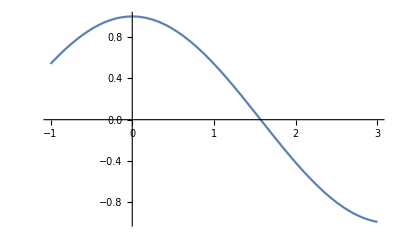
## 

## Q.2:- x^3-5*x+1^□

x0= 1

x1= 2

Nmax= 100

epsilon= 0.001

f9x0 :=1-5 x+x^3

1ithy iterations value is: 2.5

estimated error is: 0.5

2ithy iterations value is: 2.09756

estimated error is: 0.402439

3ithy iterations value is: 2.12134

estimated error is: 0.0237786

4ithy iterations value is: 2.12859

estimated error is: 0.0072456

5ithy iterations value is: 2.12842

estimated error is: 0.000166952

Return[2.12842]

root is : 2.12842

estimated error is: 8.77361×10^-7

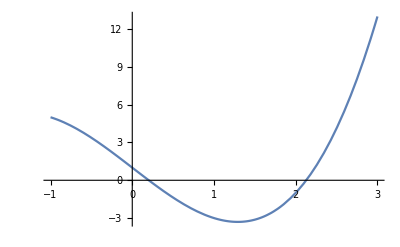

```mathematica
x0 = Input[ "Enter First guess :"];
x1 = Input[" Enter Second guess : "];
Nmax = Input["Enter maximum number of iteration :"];
eps = Input["enter the value of convergence parameter :"];
Print["x0= ", x0];
Print[ "x1= ", x1];
Print["Nmax= ", Nmax];
Print["epsilon= ", eps];
f[x_] := x^3-5*x+1^□;
Print["f9x0 :=", f[x]];


   For[i = 1, i <= Nmax, i++,
   x2 =N[x1-(f[x]/.x->x1)*(x1-x0)/((f[x]/.x->x1)-(f[x  ]/.x->x0))];
If[Abs[x1-x0] < eps, Return[x2],x0=x1;x1=x2];
    Print[ i, "ithy iterations value is: ", x2];
    Print["estimated error is: ", Abs[ x1- x0]]];

 Print["root is : " , x2];
 Print["estimated error is: ", Abs[x2 -x1]];
 Plot[f[x], {x,-1, 3}]
```

## Q.3:- x^3 +log[x]

x0= 1

x1= 2

Nmax= 100

epsilon= 0.0001

f9x0 :=x^3+Log[x]

1ithy iterations value is: 0.870014

estimated error is: 1.12999

2ithy iterations value is: 0.798226

estimated error is: 0.0717886

3ithy iterations value is: 0.712087

estimated error is: 0.0861382

4ithy iterations value is: 0.705004

estimated error is: 0.00708369

5ithy iterations value is: 0.70471

estimated error is: 0.000293377

6ithy iterations value is: 0.704709

estimated error is: 8.34876×10^-7

Return[0.704709]

root is : 0.704709

estimated error is: 9.35523×10^-11

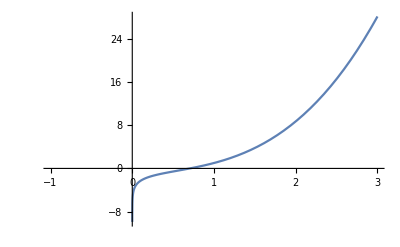

```mathematica
x0 = Input[ "Enter First guess :"];
x1 = Input[" Enter Second guess : "];
Nmax = Input["Enter maximum number of iteration :"];
eps = Input["enter the value of convergence parameter :"];
Print["x0= ", x0];
Print[ "x1= ", x1];
Print["Nmax= ", Nmax];
Print["epsilon= ", eps];
f[x_] := x^3+Log[x];
Print["f9x0 :=", f[x]];


   For[i = 1, i <= Nmax, i++,
   x2 =N[x1-(f[x]/.x->x1)*(x1-x0)/((f[x]/.x->x1)-(f[x  ]/.x->x0))];
If[Abs[x1-x0] < eps, Return[x2],x0=x1;x1=x2];
    Print[ i, "ithy iterations value is: ", x2];
    Print["estimated error is: ", Abs[ x1- x0]]];

 Print["root is : " , x2];
 Print["estimated error is: ", Abs[x2 -x1]];
 Plot[f[x], {x,-1, 3}]
```

## Q.4 : - x^5 +x^4-3*x^3+2*x^2 +x+6

x0= 1

x1= 2

Nmax= 100

epsilon= 0.001

f9x0 :=6+x+2 x^2-3 x^3+x^4+x^5

1ithy iterations value is: 0.75

estimated error is: 1.25

2ithy iterations value is: 0.477323

estimated error is: 0.272677

3ithy iterations value is: -3.3221

estimated error is: 3.79942

4ithy iterations value is: 0.313257

estimated error is: 3.63535

5ithy iterations value is: 0.161982

estimated error is: 0.151275

6ithy iterations value is: -3.96352

estimated error is: 4.1255

7ithy iterations value is: 0.112518

estimated error is: 4.07604

8ithy iterations value is: 0.0641823

estimated error is: 0.0483357

9ithy iterations value is: -4.66189

estimated error is: 4.72607

10ithy iterations value is: 0.0434929

estimated error is: 4.70539

11ithy iterations value is: 0.0229773

estimated error is: 0.0205156

12ithy iterations value is: -5.34193

estimated error is: 5.36491

13ithy iterations value is: 0.0122996

estimated error is: 5.35423

14ithy iterations value is: 0.00166318

estimated error is: 0.0106364

15ithy iterations value is: -5.83992

estimated error is: 5.84159

16ithy iterations value is: -0.00539159

estimated error is: 5.83453

17ithy iterations value is: -0.0124296

estimated error is: 0.00703804

18ithy iterations value is: -6.22649

estimated error is: 6.21406

19ithy iterations value is: -0.0176999

estimated error is: 6.20879

20ithy iterations value is: -0.0229614

estimated error is: 0.00526148

21ithy iterations value is: -6.55713

estimated error is: 6.53417

22ithy iterations value is: -0.0271401

estimated error is: 6.52999

23ithy iterations value is: -0.0313135

estimated error is: 0.00417341

24ithy iterations value is: -6.85272

estimated error is: 6.8214

25ithy iterations value is: -0.0347494

estimated error is: 6.81797

26ithy iterations value is: -0.0381818

estimated error is: 0.00343245

27ithy iterations value is: -7.12259

estimated error is: 7.08441

28ithy iterations value is: -0.0410803

estimated error is: 7.08151

29ithy iterations value is: -0.0439765

estimated error is: 0.00289616

30ithy iterations value is: -7.37224

estimated error is: 7.32826

31ithy iterations value is: -0.0464696

estimated error is: 7.32577

32ithy iterations value is: -0.0489609

estimated error is: 0.00249139

33ithy iterations value is: -7.60533

estimated error is: 7.55637

34ithy iterations value is: -0.0511383

estimated error is: 7.55419

35ithy iterations value is: -0.0533143

estimated error is: 0.00217608

36ithy iterations value is: -7.82453

estimated error is: 7.77122

37ithy iterations value is: -0.0552396

estimated error is: 7.76929

38ithy iterations value is: -0.0571639

estimated error is: 0.00192429

39ithy iterations value is: -8.03186

estimated error is: 7.9747

40ithy iterations value is: -0.0588838

estimated error is: 7.97298

41ithy iterations value is: -0.0606029

estimated error is: 0.00171913

42ithy iterations value is: -8.22889

estimated error is: 8.16828

43ithy iterations value is: -0.0621526

estimated error is: 8.16673

44ithy iterations value is: -0.0637018

estimated error is: 0.00154915

45ithy iterations value is: -8.41685

estimated error is: 8.35315

46ithy iterations value is: -0.0651085

estimated error is: 8.35174

47ithy iterations value is: -0.0665149

estimated error is: 0.00140631

48ithy iterations value is: -8.59676

estimated error is: 8.53025

49ithy iterations value is: -0.0678001

estimated error is: 8.52896

50ithy iterations value is: -0.0690849

estimated error is: 0.00128481

51ithy iterations value is: -8.76948

estimated error is: 8.70039

52ithy iterations value is: -0.0702656

estimated error is: 8.69921

53ithy iterations value is: -0.0714459

estimated error is: 0.00118038

54ithy iterations value is: -8.9357

estimated error is: 8.86425

55ithy iterations value is: -0.072536

estimated error is: 8.86316

56ithy iterations value is: -0.0736258

estimated error is: 0.00108979

57ithy iterations value is: -9.09601

estimated error is: 9.02239

58ithy iterations value is: -0.0746366

estimated error is: 9.02138

59ithy iterations value is: -0.0756471

estimated error is: 0.00101056

60ithy iterations value is: -9.25094

estimated error is: 9.1753

61ithy iterations value is: -0.0765881

estimated error is: 9.17436

62ithy iterations value is: -0.0775289

estimated error is: 0.000940778

Return[-9.40093]

root is : -9.40093

estimated error is: 9.3234

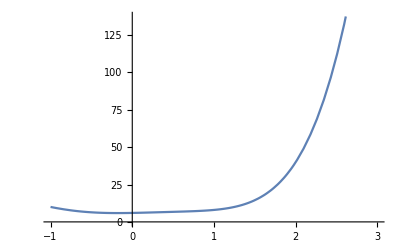

```mathematica
x0 = Input[ "Enter First guess :"];
x1 = Input[" Enter Second guess : "];
Nmax = Input["Enter maximum number of iteration :"];
eps = Input["enter the value of convergence parameter :"];
Print["x0= ", x0];
Print[ "x1= ", x1];
Print["Nmax= ", Nmax];
Print["epsilon= ", eps];
f[x_] := x^5 +x^4-3*x^3+2*x^2 +x+6;
Print["f9x0 :=", f[x]];


   For[i = 1, i <= Nmax, i++,
   x2 =N[x1-(f[x]/.x->x1)*(x1-x0)/((f[x]/.x->x1)-(f[x  ]/.x->x0))];
If[Abs[x1-x0] < eps, Return[x2],x0=x1;x1=x2];
    Print[ i, "ithy iterations value is: ", x2];
    Print["estimated error is: ", Abs[ x1- x0]]];

 Print["root is : " , x2];
 Print["estimated error is: ", Abs[x2 -x1]];
 Plot[f[x], {x,-1, 3}]
```

## Q.5:- x*e^x-Cos[x]

x0= 1

x1= 2

Nmax= 30

epsilon= 0.0001

f9x0 :=ⅇ^x x-Cos[x]

1ithy iterations value is: 0.832673

estimated error is: 1.16733

2ithy iterations value is: 0.728779

estimated error is: 0.103894

3ithy iterations value is: 0.562401

estimated error is: 0.166377

4ithy iterations value is: 0.524782

estimated error is: 0.0376189

5ithy iterations value is: 0.518014

estimated error is: 0.00676874

6ithy iterations value is: 0.517759

estimated error is: 0.0002547

7ithy iterations value is: 0.517757

estimated error is: 1.50138×10^-6

Return[0.517757]

root is : 0.517757

estimated error is: 3.22103×10^-10

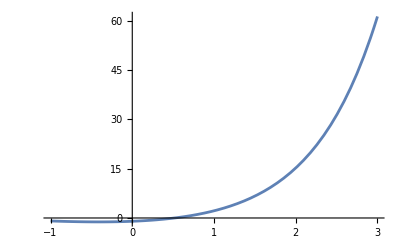
Z -Graphics-

```mathematica
x0 = Input[ "Enter First guess :"];
x1 = Input[" Enter Second guess : "];
Nmax = Input["Enter maximum number of iteration :"];
eps = Input["enter the value of convergence parameter :"];
Print["x0= ", x0];
Print[ "x1= ", x1];
Print["Nmax= ", Nmax];
Print["epsilon= ", eps];
f[x_] :=x*ⅇ^x -Cos[x];
Print["f9x0 :=", f[x]];


   For[i = 1, i <= Nmax, i++,
   x2 =N[x1-(f[x]/.x->x1)*(x1-x0)/((f[x]/.x->x1)-(f[x  ]/.x->x0))];
If[Abs[x1-x0] < eps, Return[x2],x0=x1;x1=x2];
    Print[ i, "ithy iterations value is: ", x2];
    Print["estimated error is: ", Abs[ x1- x0]]];

 Print["root is : " , x2];
 Print["estimated error is: ", Abs[x2 -x1]];
 Plot[f[x], {x,-1, 3}]Z
```